```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/data_test_largesize/test_large_size","Table"];
n:=Length[codbar]-5
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[2]]},{i,1,n,1}];
amp2=Table[{d[[i]],codbar[[i]][[4]]},{i,1,n,1}];
amp3=Table[{d[[i]],codbar[[i]][[6]]},{i,1,n,1}];
ang1=Table[{d[[i]],codbar[[i]][[1]]/(2π)},{i,1,n,1}];
ang2=Table[{d[[i]],codbar[[i]][[3]]/(2π)},{i,1,n,1}];
ang3=Table[{d[[i]],codbar[[i]][[5]]/(2π)},{i,1,n,1}];
```

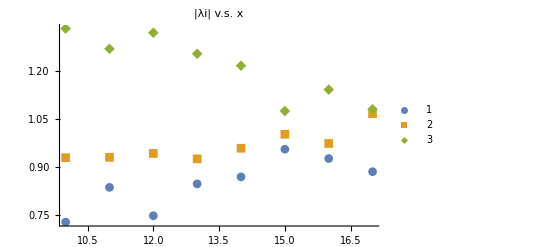

```mathematica
ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
```

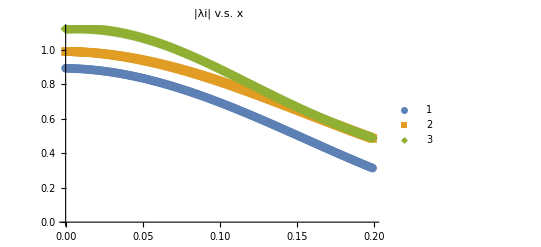

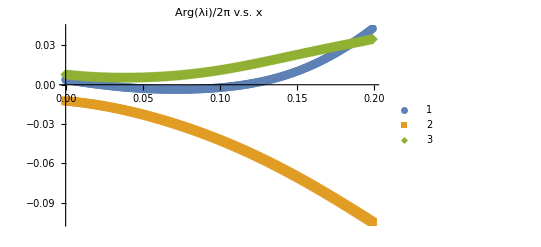

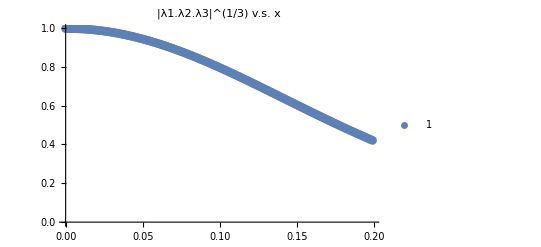

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/data_test_largesize/test_large_size","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];

λ1=Table[codbar[[i]][[3]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[4]],{i,1,n,1}];
λ2=Table[codbar[[i]][[5]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[6]],{i,1,n,1}];
λ3=Table[codbar[[i]][[7]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[8]],{i,1,n,1}];
amp1=Table[{d[[i]],Abs[λ1][[i]]},{i,1,n,1}];
amp2=Table[{d[[i]],Abs[λ2][[i]]},{i,1,n,1}];
amp3=Table[{d[[i]],Abs[λ3][[i]]},{i,1,n,1}];
ang1=Table[{d[[i]],Arg[λ1][[i]]/(2π)},{i,1,n,1}];
ang2=Table[{d[[i]],Arg[λ2][[i]]/(2π)},{i,1,n,1}];
ang3=Table[{d[[i]],Arg[λ3][[i]]/(2π)},{i,1,n,1}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]
```